# Lab 9: Spectroscopy

J.R. Powers-Luhn
jpowersl@vols.utk.edu
Station 4
Partner: Eric Francis

```mathematica
datafolder=NotebookDirectory[]<>"data/";
```

```mathematica
numchannels[filename_]:=ToExpression[StringSplit[StringSplit[Import[datafolder<>filename],"\n"][[12]]][[2]]]
counttime[filename_]:=ToExpression[StringSplit[StringSplit[Import[datafolder<>filename],"\n"][[10]]][[1]]]
```

```mathematica
numchannels["background2.spe"]
counttime["background2.spe"]
```

1023

600

```mathematica
loaddata[filename_]:=ToExpression[StringSplit[Import[datafolder<>filename],"\n"][[13;;numchannels[filename]+12]]]
```

```mathematica
bgcorrspec[filename_,bgfile_]:=loaddata[filename]/counttime[filename]-loaddata[bgfile]/counttime[bgfile];
```

```mathematica
plotpairs[filename_,bgfile_]:=Multicolumn[Join[Range[0,10,10/numchannels[filename]],bgcorrspec[filename,bgfile]],2]//First
```

```mathematica
plotspec[filename_,bgfile_]:=ListPlot[plotpairs[filename,bgfile]]
```

```mathematica
gauss[x_,y_,A_,mean_,sigma_]:=y+A/(√(2 π sigma^2))ⅇ^((-(x-mean)^2)/(2 sigma^2));
```

Assembled NaI(Tl) Detector: Setup and Spectral Analysis

1. For each spectrum collected, determine the peak position by averaging over the peak. The answer should be in channel number.

Background

```mathematica
file="background2.Spe";
bgdata=loaddata[file];
bgtime=600;
```

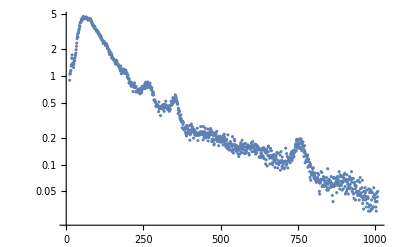

```mathematica
ListLogPlot[bgdata/bgtime]
```

Cs-137

```mathematica
file="cs137part1-15.Spe";
data=loaddata[file];
time=90;
pk=FindPeaks[data/time-bgdata/bgtime,10,10^-5,1]//N
```

{{20.,6.49389},{82.,1.68833},{201.,1.34833},{353.,5.91222}}

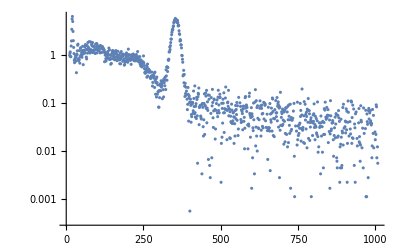

```mathematica
ListLogPlot[data/time-bgdata/bgtime,ImageSize->Full]
```

```mathematica
truecr=data/time-bgdata/bgtime;
Total[truecr[[300;;400]]*Range[300,400]]/Total[Range[300,400]]//N
```

1.61604

```mathematica
201/353*662//N
```

376.946

Co-60

```mathematica
file="co60part1.Spe";
data=loaddata[file];
time=90;
pk=FindPeaks[data/time-bgdata/bgtime,5,10^-8,10]//N
```

{{617.,24.0922},{693.,18.6911}}

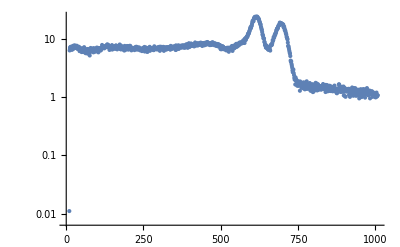

```mathematica
ListLogPlot[data/time-bgdata/bgtime,ImageSize->Full]
```

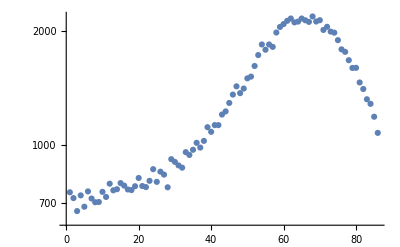

```mathematica
ListLogPlot[data[[550;;635]]]
```

```mathematica
NonlinearModelFit[Multicolumn[Join[Range[550,633],data[[550;;635]]],2]//First,gauss[x,42,A,m,s],{A,m,s},x]
```

NonlinearModelFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

FittedModel[42+0.398942 ⅇ^(-0.5 (-1.+x)^2)]

From this attempt to fit a simple Gaussian to a pretty obvious peak, it seems that this approach needs some refinement. I was unable to get a convergent fit; this could be because of the low-resolution detector.

Cd-109

```mathematica
file="cd109part1.Spe";
data=loaddata[file];
time=90;
pk=FindPeaks[data/time-bgdata/bgtime,50,10^-58,400]//N
```

{{14.,526.591}}

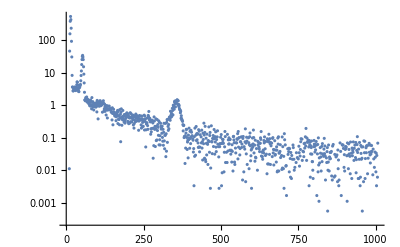

```mathematica
ListLogPlot[data/time-bgdata/bgtime,ImageSize->Full]
```

Ba-133

```mathematica
file="ba133part1.Spe";
data=loaddata[file];
time=90;
pk=FindPeaks[data/time-bgdata/bgtime,10,10^-85,8]
```

{{19,302507/600},{90,14881/900},{196,138641/1800}}

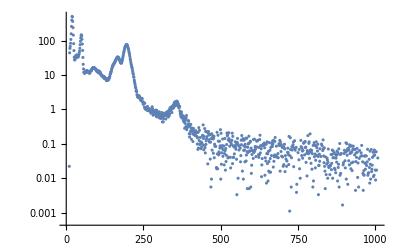

```mathematica
ListLogPlot[data/time-bgdata/bgtime,ImageSize->Full]
```

```mathematica
200/353*662//N
```

375.071

2. Make a properly formatted table in Mathematica listing the source, the emission energy, and the peak position determined from step one.

```mathematica
td={
{"Ba-133",384,196},
{"Cd-109",88.04,14},
{"Co-60",1173,617},
{"Co-60",1332,693},
{"Cs-137",661.7,353}
};
```

```mathematica
TableForm[td,TableHeadings->{None,{"Isotope","E_γ (keV)","Peak Channel"}}]
```

Isotope | E_γ (keV) | Peak Channel
Ba-133 | 384 | 196
Cd-109 | 88.04 | 14
Co-60 | 1173 | 617
Co-60 | 1332 | 693
Cs-137 | 661.7 | 353

3. From the data within the table, conduct a first order polynomial fit on the data to find the voltage to energy conversion.

```mathematica
peakfitdata=td[[;;,2;;3]]
firstorder=LinearModelFit[peakfitdata,{1,x},x]
```

{{384,196},{88.04,14},{1173,617},{1332,693},{661.7,353}}

FittedModel[-20.0162+0.542243 x]

4. Now try a second order polynomial.

```mathematica
secondorder=LinearModelFit[peakfitdata,{1,x,x^2},x]
```

FittedModel[-41.5701+0.642314 x-0.0000684871 x^2]

5. Plot the data (channel number vs. energy) along with the first and second order polynomial fits on the same, properly formatted, plot.

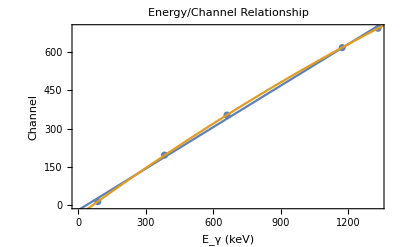

```mathematica
lp=ListPlot[peakfitdata,ImageSize->Full,Frame->True,FrameLabel->{Style["E_γ (keV)",20],Style["Channel",20]},PlotLabel->Style["Energy/Channel Relationship",24],PlotLegends->Placed[{"Measured Peaks"},{0.15,0.85}],FrameTicksStyle->Directive[16]];
fp=Plot[{firstorder[x],secondorder[x]},{x,0,1400},PlotLegends->Placed[{"First-order fit","Second-order fit"},{0.15,0.85}]];
Show[lp,fp]
```

6. In a text-style cell, discuss whether the first order or second order polynomial fit better describes the data and why. Further discuss how non-proportional the NaI(Tl) detector is.

```mathematica
firstorder["RSquared"]
```

0.998333

```mathematica
secondorder["RSquared"]
```

0.999993

It is visually apparent that the second order polynomial is a better fit for the data than the first order polynomial. This is to be expected as first-order fits are a subset of second-order fits. Some nonlinearity is expected, and this is compounded by the inaccuracy of the detector. That said, the first order fit is still very good, indicating that the response of this detector is still essentially linear.

7. Using the best fit to the data, convert the spectrum from counts vs. channel number to counts vs. energy for the Cs-137 spectrum.

```mathematica
file="cs137part1-15.Spe";
data=loaddata[file];
time=90;
chtoe=LinearModelFit[Multicolumn[Join[peakfitdata[[;;,2]],peakfitdata[[;;,1]]],2]//First,{1,x,x^2},x]
```

FittedModel[66.4153+1.54 x+0.000412287 x^2]

```mathematica
energies=Table[chtoe[x],{x,Length[data]}];
```

8. Plot the Cs-137 energy spectrum against the HPGe and CZT Cs-137 energy spectra.

1023

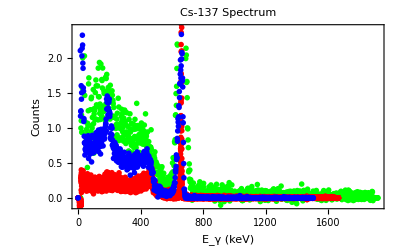

```mathematica
naiplotdata=Multicolumn[Join[plotpairs["cs137part1-15.Spe","Background2.Spe"][[;;,1]]*662/(10/2^10*353),plotpairs["cs137part1-15.Spe","Background2.Spe"][[;;,2]]],2]//First;
naiplot=ListPlot[naiplotdata,Frame->True,FrameLabel->{Style["E_γ (keV)",20],Style["Counts",20]},FrameTicksStyle->Directive[16],ImageSize->Full,PlotLabel->Style["Cs-137 Spectrum",24],PlotStyle->Green,PlotLegends->Placed[{"NaI(Tl)"},{0.85,0.85}],PlotMarkers->Style["*",Medium]];
hpgeplot=ListPlot[Multicolumn[Join[plotpairs["Cs137.Spe","bkg.Spe"][[;;,1]]*662/(10/2^14*6510),plotpairs["Cs137.Spe","bkg.Spe"][[;;,2]]],2]//First,PlotStyle->Red,PlotLegends->Placed[{"HPGe"},{0.85,0.85}],PlotMarkers->Style["*",Medium]];
numchannels["Cs_137_120sec.Spe"]
cztplot=ListPlot[Multicolumn[Join[plotpairs["Cs_137_120sec.Spe","Background_600sec.Spe"][[;;,1]]*662/(10/2^10*450),plotpairs["Cs_137_120sec.Spe","Background_600sec.Spe"][[;;,2]]],2]//First,PlotStyle->Blue,PlotLegends->Placed[{"CZT"},{0.85,0.85}],PlotMarkers->Style["*",Medium]];
Show[naiplot,hpgeplot,cztplot]
```

As expected, the HPGe

9. Below the plot, and in a text-style cell, discuss what you see on the plot in step 8. Describe the shape of each spectra and the resolution of each.

Here’s what I see: the HPGe detector has the best resolution available, and its spectrum features narrow peaks at the energies corresponding to the Cesium spectrum--most notably 662 keV. Coming next in the lineup is another semiconductor detector--CZT, or cadmium zinc telluride. The CZT has a larger band gap (1.2-2.2 eV) than the HPGe crystals, meaning that its resolution is lower. This causes the peaks to undergo a gaussian broadening--making them harder to match to a specific energy and potentially overlapping nearby spectral peaks. Finally, the NaI(Tl) curve shown above has the worst resolution of the three. Distinguishing between even well-separated peaks (e.g. Co-60) becomes more difficult, or (in the case of Ba-133) impossible (see plot above). NaI(Tl) detectors do have the advantage of size, however--they can be grown very large, increasing their intrinsic efficiency.

The Need for a Preamplifier

1. For each spectrum collected with and without the preamplifier in the pulse processing chain, determined the full energy peak position in channel number units.
	a. Note: The peak may drift away for larger shaping time constants, and may even disappear. If this happens, label it as “Not Present”.

```mathematica
filenames={
"Amp05.Spe",
"Amp1.Spe",
"Amp10.Spe",
"Amp2.Spe",
"Amp3.Spe",
"Amp6.Spe",
"PreAmp-05.Spe",
"PreAmp-1.Spe",
"PreAmp-10.Spe",
"PreAmp-2.Spe",
"PreAmp-3.Spe",
"PreAmp-6.Spe"
};
```

### Shaping time = 0.5μs

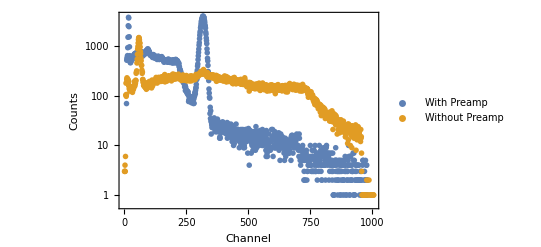

```mathematica
ListLogPlot[Map[loaddata,{"PreAmp-05.Spe","Amp05.Spe"}],ImageSize->Full,PlotLegends->Placed[{"With Preamp","Without Preamp"},{0.85,0.85}],PlotMarkers->Style["*",Medium],Frame->True,FrameLabel->{Style["Channel",20],Style["Counts",20]}]
```

```mathematica
Table[FindPeaks[loaddata[f],10,10^-5,1500],{f,{"PreAmp-05.Spe","Amp05.Spe"}}]
```

{{{18,3854},{319,4076}},{{60,1506}}}

The peak for the preamp is at channel 319; for the Amp there is no obvious peak on scale.

### Shaping time = 1μs

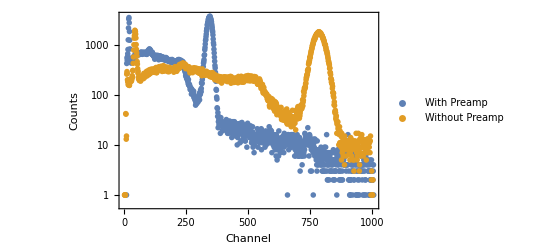

```mathematica
ListLogPlot[Map[loaddata,{"PreAmp-1.Spe","Amp1.Spe"}],ImageSize->Full,PlotLegends->Placed[{"With Preamp","Without Preamp"},{0.85,0.85}],PlotMarkers->Style["*",Medium],Frame->True,FrameLabel->{Style["Channel",20],Style["Counts",20]}]
```

```mathematica
Table[FindPeaks[loaddata[f],10,10^-5,1500],{f,{"PreAmp-1.Spe","Amp1.Spe"}}]
```

{{{20,3472},{347,3706}},{{44,1937},{788,1810}}}

The peak for the preamp is at channel 347; for the Amp it is at 788.

### Shaping time = 2μs

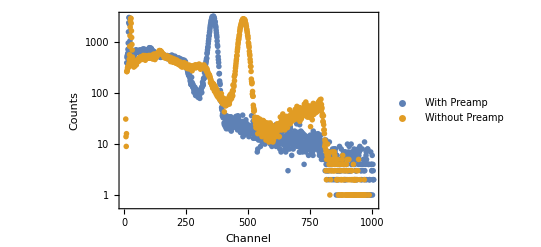

```mathematica
ListLogPlot[Map[loaddata,{"PreAmp-2.Spe","Amp2.Spe"}],ImageSize->Full,PlotLegends->Placed[{"With Preamp","Without Preamp"},{0.85,0.85}],PlotMarkers->Style["*",Medium],Frame->True,FrameLabel->{Style["Channel",20],Style["Counts",20]}]
```

```mathematica
Table[FindPeaks[loaddata[f],10,10^-5,1500],{f,{"PreAmp-2.Spe","Amp2.Spe"}}]
```

{{{20,3057},{361,3258}},{{28,2952},{484,2874}}}

The peak for the preamp is at channel 361; for the Amp it is at 484.

### Shaping time = 3μs

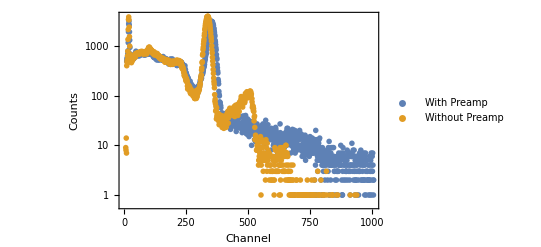

```mathematica
ListLogPlot[Map[loaddata,{"PreAmp-3.Spe","Amp3.Spe"}],ImageSize->Full,PlotLegends->Placed[{"With Preamp","Without Preamp"},{0.85,0.85}],PlotMarkers->Style["*",Medium],Frame->True,FrameLabel->{Style["Channel",20],Style["Counts",20]}]
```

```mathematica
Table[FindPeaks[loaddata[f],10,10^-5,1500],{f,{"PreAmp-3.Spe","Amp3.Spe"}}]
```

{{{20,3138},{353,3149}},{{19,3846},{338,3999}}}

The peak for the preamp is at channel 353; for the Amp it is at 338.

### Shaping time = 6μs

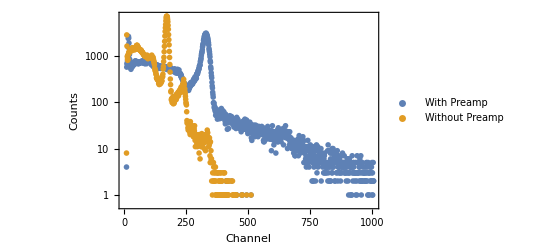

```mathematica
ListLogPlot[Map[loaddata,{"PreAmp-6.Spe","Amp6.Spe"}],ImageSize->Full,PlotLegends->Placed[{"With Preamp","Without Preamp"},{0.85,0.85}],PlotMarkers->Style["*",Medium],Frame->True,FrameLabel->{Style["Channel",20],Style["Counts",20]}]
```

```mathematica
Table[FindPeaks[loaddata[f],10,10^-5,1500],{f,{"PreAmp-6.Spe","Amp6.Spe"}}]
```

{{{18,2603},{331,3071}},{{53,1679},{172,7106}}}

The peak for the preamp is at channel 331; for the Amp it is at 172.

### Shaping time = 10μs

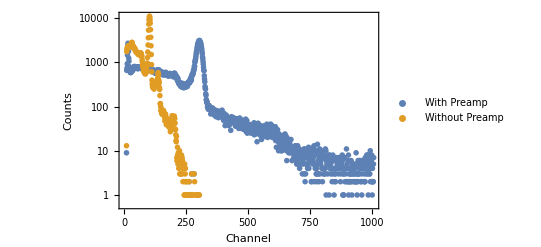

```mathematica
ListLogPlot[Map[loaddata,{"PreAmp-10.Spe","Amp10.Spe"}],ImageSize->Full,PlotLegends->Placed[{"With Preamp","Without Preamp"},{0.85,0.85}],PlotMarkers->Style["*",Medium],Frame->True,FrameLabel->{Style["Channel",20],Style["Counts",20]}]
```

```mathematica
Table[FindPeaks[loaddata[f],10,10^-5,1500],{f,{"PreAmp-10.Spe","Amp10.Spe"}}]
```

{{{16,2696},{305,3131}},{{32,2827},{103,11078}}}

The peak for the preamp is at channel 305; for the Amp it is at 103.

2. Make a properly formatted table in Mathematica that includes the shaping time, peak position with preamp, and peak position without preamp.

```mathematica
headers={"Shaping Time (μs)","Preamp Peak Channel","Amp Peak Channel"};
td={
{0.5,319,"NA"},
{1, 347,788},
{2,361,484},
{3,353,338},
{6,331,172},
{10,305,103}
};
TableForm[td,TableHeadings->{None,headers}]
```

Shaping Time (μs) | Preamp Peak Channel | Amp Peak Channel
0.5 | 319 | NA
1 | 347 | 788
2 | 361 | 484
3 | 353 | 338
6 | 331 | 172
10 | 305 | 103

3. Investigating the data contained within the table, discuss the trends observed with and without the preamplifier present in a text-style cell. Theorize the origin of the differences between the two datasets, [sic] and further comment on why the use of a preamplifier is necessary.

The detectors we use do not integrate voltage; instead they collect charge. The preamplifier’s role is to convert these current pulses into a voltage, but this voltage takes the form of a slowly decaying, quasi-square wave pulse. The amplifier then takes this voltage and converts it into a quasi-gaussian pulse with amplitude equal to the charge collected in the detector by acting as a crude differentiator.

Without the preamplifier, changing the shaping time of the amplifier causes it to collect charge over a different period of time. If that time is shorter, then a smaller voltage builds up in the output signal, which the MCA sees as a lower energy channel. With the preamplifier in line, this effect does not occur. We see this happening

Integral Pulse Height Spectrum

1. Make a 2D list of data of LLD (x-value) and counts (y-value).

```mathematica
iphsdata=Multicolumn[Join[{0,0.25,0.50,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1,2.3,2.5,2.7,2.9,3.1,3.3,3.5,3.7,3.9,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.0,5.1},{84125,69417,67078,61940,56896,51316,46862,43257,39783,37589,35336,33244,30825,29532,28846,27907,26990,18696,4899,2905,2648,2619,2532,2439,2361,2211,2051,1951,1967,1924,1782}],2]//First;
```

2. Change the collected Cs-137 spectra in the first part of the lab from counts vs. channel number to counts vs. voltage.

3. Plot the 2D list of data, which is a crude integral pulse height spectrum, against the quality differential pulse height spectrum.
	a. You may try and connect the dots between data points using the “Interpolation” option in Mathematica for graphing purposes so it is easier to compare the two spectra.

```mathematica
ihpsplot=ListPlot[iphsdata,Joined->True,Frame->True,FrameLabel->{Style["LLD",20],Style["Counts",20]},FrameTicksStyle->Directive[16],PlotLabel->Style["Integral Pulse Height Spectrum",24],ImageSize->Full,PlotRange->{{0,5.1},{0,90000}}]
cs137plot=ListPlot[plotpairs["Cs137.Spe","bkg.Spe"],Joined->True,Frame->True,FrameLabel->{Style["LLD",20],Style["Counts",20]},FrameTicksStyle->Directive[16],PlotLabel->Style["Cs-137 Spectrum",24],ImageSize->Full,PlotRange->{{0,5.1},{0,5}}]
```

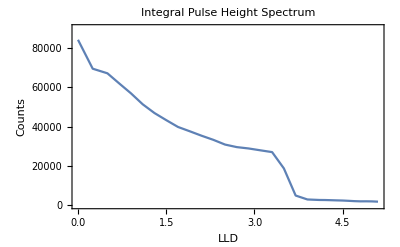

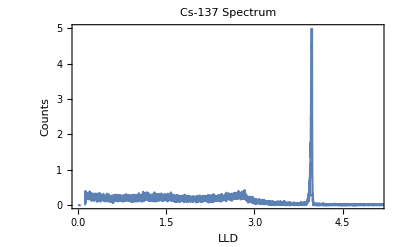

4. Using the drawing tools, correlate the shape of each spectra with each other.